```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Ben\Dropbox\Bayesian book\Figures

```mathematica
toPiecewise[wts_,x_]:=Piecewise[MapIndexed[{#1,x==#2[[1]]}&,wts]]
vRatePrior= {1,0.5,0.25,0.1,0.1,0.05};
vRatePosterior= {0.1,0.2,0.25,1,2,0.75};
vRatePosterior = vRatePosterior/Total@vRatePosterior;
vRatePrior = vRatePrior/Total@vRatePrior;
```

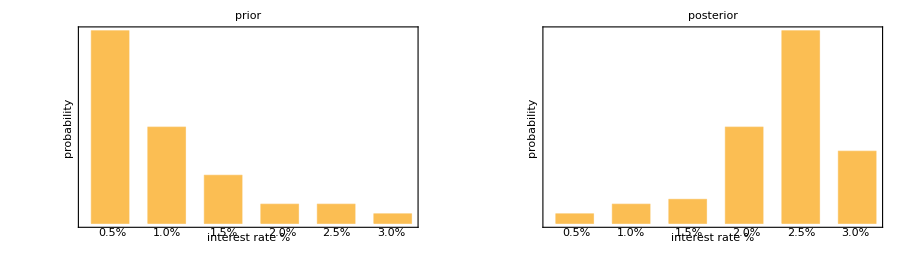

```mathematica
gPrior= BarChart[vRatePrior,BarSpacing->Large,FrameLabel->{"interest rate %", "probability"},FrameTicks->{False,False},Frame->{True,True,False,False},PlotLabel->"prior",Epilog->{Text["0.5%",Scaled[{0.1,-.03}]],Text["1.0%",Scaled[{0.26,-.03}]],Text["1.5%",Scaled[{0.43,-.03}]],Text["2.0%",Scaled[{0.60,-.03}]],Text["2.5%",Scaled[{0.76,-.03}]],Text["3.0%",Scaled[{0.92,-.03}]]}];
gPosterior = BarChart[vRatePosterior,BarSpacing->Large,FrameLabel->{"interest rate %", "probability"},FrameTicks->{False,False},PlotLabel->"posterior",Frame->{True,True,False,False},Epilog->{Text["0.5%",Scaled[{0.1,-.03}]],Text["1.0%",Scaled[{0.26,-.03}]],Text["1.5%",Scaled[{0.43,-.03}]],Text["2.0%",Scaled[{0.60,-.03}]],Text["2.5%",Scaled[{0.76,-.03}]],Text["3.0%",Scaled[{0.92,-.03}]]}];
gPriorAndPosterior=Show[GraphicsRow[{gPrior,gPosterior}],ImageSize->900]
```

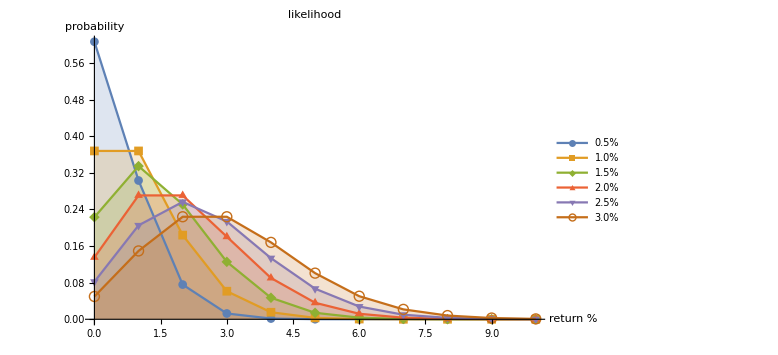

```mathematica
gLikelihood = Show[DiscretePlot[Evaluate@Table[PDF[PoissonDistribution[λ],k],{λ,{0.5,1,1.5,2.0,2.5,3}}],{k,0,10},PlotRange->All,PlotMarkers->Automatic,Joined->True,PlotLegends->Placed[{"0.5%","1.0%","1.5%","2.0%","2.5%","3.0%"},Center],AxesLabel->{"return %","probability"},BaseStyle->{FontSize->14},PlotLabel->"likelihood"],ImageSize->Large]
```

```mathematica
posteriorDistribution=ProbabilityDistribution[toPiecewise[vRatePosterior],{x,1,6,1}];
```

```mathematica
vLambda = {0.5,1.0,1.5,2.0,2.5,3.0};
priorPredictive[x_]:=Sum[PDF[PoissonDistribution[vLambda[[i]]],x]*vRatePrior[[i]],{i,1,6,1}]
posteriorPredictive[x_]:=Sum[PDF[PoissonDistribution[vLambda[[i]]],x]*vRatePosterior[[i]],{i,1,6,1}]
```

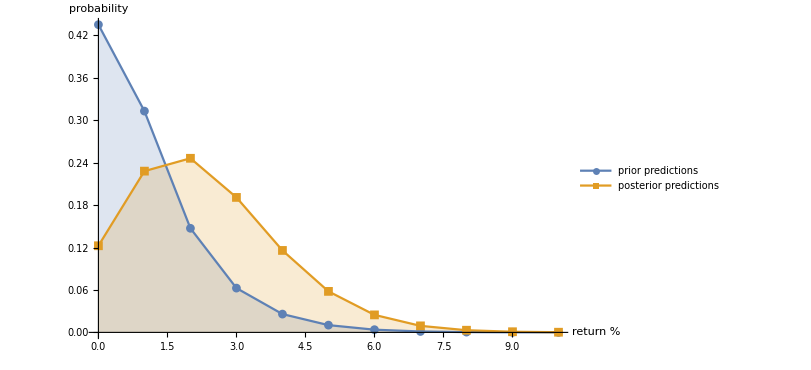

```mathematica
gPriorAndPosteriorPredictive=Show[DiscretePlot[{priorPredictive[x],posteriorPredictive[x]},{x,0,10,1},Joined->True,PlotMarkers->{Automatic, 9},AxesLabel->{"return %","probability"},Ticks->{True,True},PlotLegends->Placed[{"prior predictions","posterior predictions"},Center],BaseStyle->{FontSize->14}],ImageSize->600]
```

```mathematica
Sum[priorPredictive[x],{x,0,100}]
Sum[posteriorPredictive[x],{x,0,100}]
```

1.

```mathematica
Export["Posterior_priorPosteriorInterestRate.pdf",gPriorAndPosterior]
```

Posterior_priorPosteriorInterestRate.pdf

```mathematica
Export["Posterior_likelihoodInterestRate.pdf",gLikelihood]
```

Posterior_likelihoodInterestRate.pdf

```mathematica
Export["Posterior_priorPosteriorPredictiveInterestRate.pdf",gPriorAndPosteriorPredictive]
```

Posterior_priorPosteriorPredictiveInterestRate.pdf

C:\Users\Ben\Dropbox\Bayesian book\Figures

```mathematica
data=Table[Evaluate@Table[PDF[PoissonDistribution[λ],k],{λ,{0.5,1,1.5,2.0,2.5,3}}]*vRatePrior,{k,0,10}]
```

{{0.303265,0.0919699,0.0278913,0.00676676,0.00410425,0.00124468},{0.151633,0.0919699,0.0418369,0.0135335,0.0102606,0.00373403},{0.0379082,0.0459849,0.0313777,0.0135335,0.0128258,0.00560105},{0.00631803,0.0153283,0.0156888,0.00902235,0.0106882,0.00560105},{0.000789753,0.00383208,0.00588331,0.00451118,0.00668009,0.00420078},{0.0000789753,0.000766416,0.00176499,0.00180447,0.00334005,0.00252047},{6.58128×10^-6,0.000127736,0.000441249,0.00060149,0.00139169,0.00126024},{4.70091×10^-7,0.000018248,0.0000945533,0.000171854,0.000497031,0.000540101},{2.93807×10^-8,2.281×10^-6,0.0000177287,0.0000429636,0.000155322,0.000202538},{1.63226×10^-9,2.53444×10^-7,2.95479×10^-6,9.54746×10^-6,0.000043145,0.0000675126},{8.16131×10^-11,2.53444×10^-8,4.43218×10^-7,1.90949×10^-6,0.0000107863,0.0000202538}}

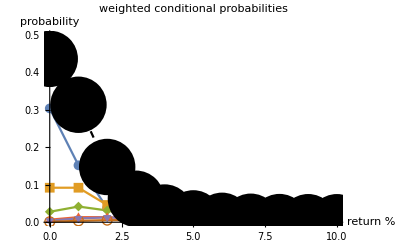

```mathematica
gPriorPredictive1=Show[ListLinePlot[Thread[{Range[11]-1,#}]&/@(Transpose@data),PlotRange->{Automatic,{0,0.5}},AxesLabel->{"return %","probability"},PlotLabel->"weighted conditional probabilities",BaseStyle->{FontSize->14},PlotMarkers->{Automatic, 10},PlotLegends->Placed[{"0.5%","1.0%","1.5%","2.0%","2.5%","3.0%"},Center]],DiscretePlot[priorPredictive[x],{x,0,10},Joined->True,Filling->None,PlotLegends->Placed[{"prior predictive"},Center],PlotStyle->{Black,Dashed},AxesLabel->{"return %","probability"},BaseStyle->{FontSize->14},PlotMarkers->Style["•", FontSize -> 58]]]
```

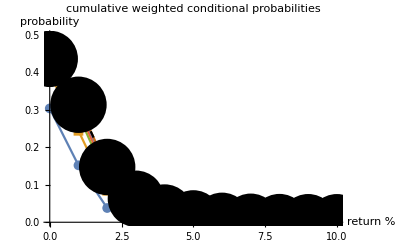

```mathematica
gPriorPredictive2=Show[ListLinePlot[Thread[{Range[11]-1,#}]&/@Accumulate[Transpose[data]],PlotLabel->"cumulative weighted conditional probabilities",AxesLabel->{"return %","probability"},BaseStyle->{FontSize->14},PlotMarkers->{Automatic, 10},PlotRange->{Automatic,{0,0.5}},PlotLegends->Placed[{"0.5%","1.0%","1.5%","2.0%","2.5%","3.0%"},Center]],DiscretePlot[priorPredictive[x],{x,0,10},Joined->True,Filling->None,PlotStyle->{Black,Dashed},PlotLegends->Placed[{"prior predictive"},Center],PlotMarkers->Style["•", FontSize -> 58]]]
```

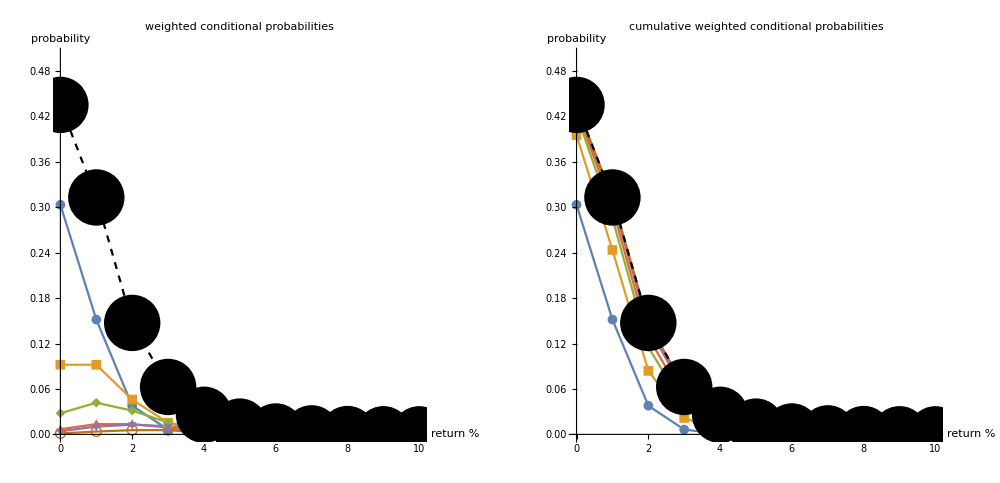

```mathematica
gBuilding=Show[GraphicsRow[{gPriorPredictive1,gPriorPredictive2}],ImageSize->1000]
```

```mathematica
Export["Posterior_priorBuildInterestRate.pdf",gBuilding]
```

Posterior_priorBuildInterestRate.pdf